# Single Field Potential

Bounce

61.367               2                                       251.249              2                             647.505               2
BounceFunction[<|Action -> 8202.59, Bounce -> (Piecewise[{{2.41202, #1 < 7.25778}, {4.74205 - ------ - 0.0221171 #1 , 7.25778 <= #1 < 9.20403}, {9.22494 - ------- - 0.048576 #1 , <<1>>}, <<6>>, {-5.69715 + ------- + 0.0125318 #1 , 12.9408 <= #1 < 15.0767}}] & ), <<11>>, Radii -> {7.25778, 9.20403, 9.95431, 10.4621, 10.8871, 11.2897, 11.7126, 12.2139, 12.9408, 15.0767}|>]
                                                                                                 2                                                             2                                                  2
                                                                                               #1                                                            #1                                                 #1

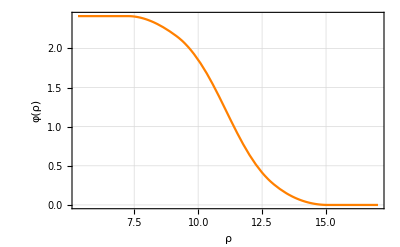

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<FindBounce.m
U1[ϕ_]:=Block[{αs = .9,V},V = 1/2(ϕ)^2-1/2(ϕ)^3+αs/8 (ϕ)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
PB1 =  FindBounce[ U1[ϕ],{ϕ},{Extrema1[[1]],Extrema1[[3]]},  "Segments"->9]
BouncePlot[PB1]
```

Potential

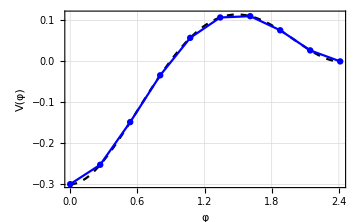

```mathematica
plotU = Plot[U1[Extrema1[[3]]-ϕ],{ϕ,0,Extrema1[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
Show[plotU,ListPlot[Transpose@{PB1["PathLongitudinal"],PB1["Potential"]},Joined->True,Mesh->All,PlotStyle->Blue]]
```